```mathematica
(* Returns a Nested list of pair of points representing each line in polygon*)
lineList[list_]:=Partition[Append[list,First[list]],2,1];
```

```mathematica
(*Returns a Vector for a line between two points*)
vector[{{x1_,y1_},{x2_,y2_}}]:={x2-x1,y2-y1}
```

Reference : https : // demonstrations.wolfram.com/SegmentIntersection

```mathematica
(*The parametric equation of the line containing the points a and b is a+λ (b-a), where 0≤λ≤1 for points between a and b. The value of λ is given by*)λ[{a_,b_}][p_]:=((a-p).(a-b))/((a-b).(a-b))
```

```mathematica
(*for p on the line. For p not on the line, λ gives the closest point on the line.*)
(*Two lines, Subscript[L, 1] containing the points a and b with line Subscript[L, 2] containing the points c and d, intersect at a point ⟺ |{a-b,c-d}|≠0.  Compute the intersection point:*)
LineIntersectionPoint[{{a_,b_},{c_,d_}}]:=(Det[{a,b}] (c-d)-Det[{c,d}] (a-b))/Det[{a-b,c-d}]
```

```mathematica
(*Use |{a-b,c-d}|≠0 along with the condition 0≤λ≤1 to determine whether two segments intersect:*)
SegmentIntersectionQ[{p1:{a_,b_},p2:{c_,d_}}]:=
If[Det[{a-b,c-d}]==0,False,
Module[{p=LineIntersectionPoint[{p1,p2}]},0≤ λ[p1][p]≤ 1 &&0≤ λ[p2][p]≤ 1]]
```

```mathematica
(* Returns the angle made in [o,2Pi) Range*)
(*Reference: https://mathematica.stackexchange.com/questions/111629/calculating-the-angle-between-the-line-joining-two-points-and-the-x-axis*)
getAngle[{{x1_,y1_},{x2_,y2_}}]:=Mod[ArcTan[x2-x1,y2-y1],2 π]
```

```mathematica
vertexList[list_]:=Partition[Join[list,list⟦1;;2⟧],3,1]
```

```mathematica
(*true if pt  is inside polygon*)
testpoint[poly_,pt_]:=Round[(Total@Mod[(#-RotateRight[#])&@(ArcTan@@(pt-#)&/@poly),2 Pi,-Pi]/2/Pi)]≠0
```

```mathematica
Manipulate[Module[{o,boundpoly,poly1,poly2,listofAllLines,sortedList,sortedText,JList={},InfinteLine,i,j,tempList,output,prevOut,printJList,tp},
(*Obsctale Centroids*)
o={o1,o2};

(*Obstacle and Boundary Polygon Points*)
boundpoly=5CirclePoints@4;
poly1=(o1+#)&/@(CirclePoints@6);
poly2=(o2+#)&/@(CirclePoints@4);

(*Line Parallel to X axis*)
InfinteLine={p,{Max@(#⟦1⟧&/@(Join[boundpoly,poly1,poly2])),p⟦2⟧}};

(*List of all lines in space*)
listofAllLines=Join[lineList@(Reverse@boundpoly),lineList@(poly1),lineList@(poly2)];

sortedList=N@Sort[Join[vertexList@boundpoly,vertexList@poly1,vertexList@poly2],If[getAngle[{p,#1⟦2⟧}]≠  getAngle[{p,#2⟦2⟧}],getAngle[{p,#1⟦2⟧}]<getAngle[{p,#2⟦2⟧}],Norm[p-#1⟦2⟧]<Norm[p-#2⟦2⟧]] &];

(*get the intersection of lines for the Infinteline*)
If[SegmentIntersectionQ[{InfinteLine,#}]==True,AppendTo[JList,#]]&/@listofAllLines;
(*Store the sorted values in J list*)
JList=Sort[JList,EuclideanDistance[InfinteLine,#]<EuclideanDistance[InfinteLine,#]&];

tempList={};
printJList={};
For[i=1,i≤ Length@sortedList,i++,
AppendTo[printJList,JList];
If[intersectInteriorQRev2[p,sortedList⟦i⟧],output=False,

If[Or[i==1,Not[pointOnSegmentQ[{p,sortedList⟦i,2⟧},sortedList⟦i,1⟧]]],

If[(Or@@(And[(SegmentIntersectionQ[{{p,sortedList⟦i,2⟧},#}]),LineIntersectionPoint[{{p,sortedList⟦i,2⟧},#}]≠ #⟦1⟧]&/@JList)),output=False,output=True]
,If[prevOut,False,
If[Or@@((SegmentIntersectionQ[{#,{sortedList⟦i,1⟧,sortedList⟦i,2⟧}}])&/@JList),output=False,output=True];
];
];
];
prevOut=output;
If[output,
AppendTo[tempList,sortedList⟦i,2⟧];
AppendTo[JList,{sortedList⟦i,1⟧,sortedList⟦i,2⟧}];
JList =DeleteCases[JList,{sortedList⟦i,2⟧,sortedList⟦i,3⟧}];(*Doubt*)
];
];

(*Number Text to the Sorted Lines*)
sortedText=Table[Text[i,{0,0}+Mean@{p,sortedList⟦i,2⟧}],{i,1,Length@sortedList,1}];


(**)



m=Length@printJList;
Graphics[{
(*Boundary Polygon*)
{{EdgeForm[Thin],White,Polygon@boundpoly}}
(*Lines from point P and point P*)
,{{Opacity[0.2],Blue,Line@({p,#⟦2⟧})&/@sortedList}}
,{{Blue,sortedText}}
,{{Blue,PointSize->Large,Point@p}}
(*Obstacle Polygons*)
,{{EdgeForm[Thin],Opacity[0.1],White,Polygon@poly1}}
,{{EdgeForm[Thin],Opacity[0.1],White,Polygon@poly2}}
(*Infinite Line*)
,{{Blue,Line@InfinteLine}}
(*,{{Green,Line@JList}}*)
,{{Red,Point@tempList}}
,{{Green,Line@printJList⟦s⟧}}
}]
]
,{{o1,{0,0}},3{-1,-1},3{1,1},ControlType-> Locator}
,{{o2,{2,2}},3{-1,-1},3{1,1},ControlType-> Locator}
,{{s,1,"Slider"},1,m,1,ControlType-> Slider}
,{{m,1},ControlType-> None}
,{{p,{1,-2}},3{-1,-1},3{1,1},ControlType-> Locator,Appearance->None}
]
```

```mathematica
listA = 1;
listB = {a,c,b};
AbsoluteTiming@({listA,#}&/@listB)
```

```mathematica
ClearAll["Global`*"]
```

True

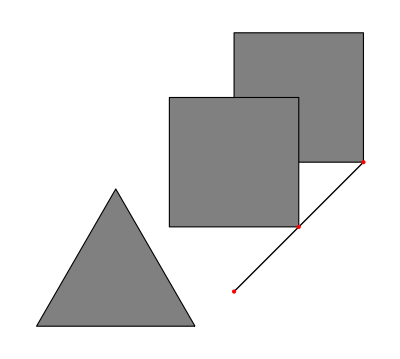

```mathematica
poly1=(#+{1,2})&/@CirclePoints[4];
poly2=(#+{-1,0})&/@CirclePoints[3];
poly3=(#+poly1⟦4⟧)&/@CirclePoints[4];

p={1+1/(√2)-√2,2-1/(√2)-√2};
j={{{3,4},{3,-4}}};
i=1;
wi=poly1⟦1⟧;
wi1=poly3⟦1⟧;
(*If[Count[SegmentIntersectionQ[N@{#,{p,wi}}]&/@(lineList@poly1),True]≠2,Print@False,Print@True];*)
pointOnSegmentQ[{p,wi},wi1]
Graphics[{EdgeForm[Thin],{Gray,Polygon@poly1,Polygon@poly2,Polygon@poly3},{Line@{p,wi},{Red,Point@{p,wi,wi1}}}}]
```

```mathematica
pointOnSegmentQ[{{x1_,y1_},{x2_,y2_}},{x3_,y3_}]:=Module[{ABv ={x2-x1,y2-y1,0},ACv={x3-x1,y3-y1,0},Kac,Kab},
If[And@@((#==0)&/@Cross[ABv,ACv]),
Kac=ABv.ACv;
Kab=ABv.ABv;
If[Kac<0,False,
If[Kac>Kab,False,
If[0<Kac<Kab,True,False]
]],False]]
```

```mathematica
l={0,0};
m={1,1};
n={2,2};
pointOnSegmentQ[{l,n},m]
```

True

```mathematica
{m,n,l}×{x,y,z}
```

```mathematica
vertexList[list_]:=Partition[Join[list,list⟦1;;2⟧],3,1]
```

```mathematica
(*Line pwi intersects interior of the obstacle of the which wi is the vertex.*)
Manipulate[po1 = ({0,-1}+#)&/@CirclePoints[4];
po2 = ({2,-2}+#)&/@CirclePoints[5];
po3 = ({2,1}+#)&/@CirclePoints[3];
po4={{0,0},{0,1},{-0.5,0.5},{-1,1},{-1,0}};
SortedList=N@Sort[Join[vertexList@po1,vertexList@po2,vertexList@po3,vertexList@po4],getAngle[{p,#1⟦2⟧}]<getAngle[{p,#2⟦2⟧}] &];
Q=intersectInteriorQRev2[p,#]&/@SortedList;
Graphics[{{EdgeForm[Thin],White,Polygon@po1,Polygon@po2,Polygon@po3,Polygon@po4},{Red,Point@p},{Blue,Line@{p,SortedList⟦s⟧⟦2⟧}},{Text[Q⟦s⟧,Mean@{p,SortedList⟦s⟧⟦2⟧}]}}]
,Control@{{s,1,"Move"},1,Length@SortedList,1,Appearance->"Open"}
,{{p,{2,0}},ControlType->Locator}]
```

```mathematica
(*True if w2 is Interior vertex from p *)
intersectInteriorQRev2[p_,{w1_,w2_,w3_}]:=getClockwiseAngle[w1,w2,w3]> getClockwiseAngle[p,w2,w3]
(*Clockwise angle bwtween tw o vectors*)
(*https://adndevblog.typepad.com/manufacturing/2012/07/finding-the-angle-between-two-vectors-along-a-given-direction-anti-clockwise-or-clockwise.html*)
getClockwiseAngle[p1_,p2_,p3_]:=Module[{a=p3-p2,b=p1-p2},
AppendTo[a,0];AppendTo[b,0];
If[Cross[a,b]⟦3⟧<0,(2Pi -VectorAngle[a,b]),VectorAngle[a,b]]
]
(*Returns if the vertex is not visible from point p *)
intersectInteriorQ[p_,{w1_,w2_,w3_}]:=Or[anglePoints[w1,w2,w3]< anglePoints[p,w2,w3],anglePoints[w1,w2,w3]< anglePoints[p,w2,w1]]
(*Returns angle between the three points*)
anglePoints[p0_,p1_,p2_]:=
Module[{a=((p1⟦1⟧-p0⟦1⟧)^2+(p1⟦2⟧-p0⟦2⟧)^2),b=((p1⟦1⟧-p2⟦1⟧)^2+(p1⟦2⟧-p2⟦2⟧)^2),c=((p2⟦1⟧-p0⟦1⟧)^2+(p2⟦2⟧-p0⟦2⟧)^2)},Mod[(ArcCos@((a+b-c)/Sqrt[4*a*b])),2Pi]]
```

```mathematica
f1=#1⟦2⟧>#2⟦2⟧&;
f2=#1⟦1⟧>#2⟦1⟧&;
Sort[{{1,1},{1,2},{2,1}},If[#1⟦1⟧≠ #2⟦1⟧,#1⟦1⟧<#2⟦1⟧,#1⟦2⟧>#2⟦2⟧]&]
```

{{1,2},{1,1},{2,1}}

```mathematica
list= {1,2,3,4};
list= DeleteCases[list,1]
```

{2,3,4}